```mathematica
SetDirectory["./Desktop/PowerGraphene/BilayerNumDiag"]
```

/home/user/Desktop/PowerGraphene/BilayerNumDiag

```mathematica
data=Import["fileL0.txt","Table"];
data//MatrixForm
```

(1 | 4. | 2.53974×10^-8
1 | 3.33333 | 4.16824×10^-7
1 | 2.85714 | 2.78958×10^-6
1 | 2.5 | 0.0000120918
1 | 2.22222 | 0.0000367784
1 | 2. | 0.0000905161
2 | 4. | 7.13223×10^-9
2 | 3.33333 | 1.02927×10^-7
2 | 2.85714 | 7.179×10^-7
2 | 2.5 | 2.99848×10^-6
2 | 2.22222 | 9.23142×10^-6
2 | 2. | 0.0000225623
3 | 4. | 3.15043×10^-9
3 | 3.33333 | 4.68115×10^-8
3 | 2.85714 | 3.18026×10^-7
3 | 2.5 | 1.3387×10^-6
3 | 2.22222 | 4.09552×10^-6
3 | 2. | 0.0000100257
5 | 4. | 9.86999×10^-10
5 | 3.33333 | 1.32433×10^-8
5 | 2.85714 | 1.09754×10^-7
5 | 2.5 | 4.67946×10^-7
5 | 2.22222 | 1.45688×10^-6
5 | 2. | 3.56891×10^-6
7 | 4. | 5.48481×10^-10
7 | 3.33333 | 8.46152×10^-9
7 | 2.85714 | 5.79094×10^-8
7 | 2.5 | 2.44125×10^-7
7 | 2.22222 | 7.47993×10^-7
7 | 2. | 1.83301×10^-6
10 | 4. | 2.59171×10^-10
10 | 3.33333 | 4.06583×10^-9
10 | 2.85714 | 2.81035×10^-8
10 | 2.5 | 1.19031×10^-7
10 | 2.22222 | 3.64543×10^-7
10 | 2. | 8.95646×10^-7)

```mathematica
Show[ListPlot3D[data,Mesh->All,AxesLabel->{a,g}],ListPointPlot3D[data]]
```

-Graphics3D-

```mathematica
FindFit[data,2Log[A/a]-G ginv,{A,G},{a,ginv}]
Table[2Log[A/a]-G ginv/.%,{a,1,10,1},{ginv,0.5,2,0.1}]//MatrixForm
Show[ListPlot3D[%,Mesh->All,AxesLabel->{a,g}],ListPointPlot3D[%]]
Show[ListPlot3D[data,Mesh->All,AxesLabel->{a,g}],ListPointPlot3D[data]]
```

{A→3.57857,G→8.50549×10^-6}

(2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54992 | 2.54991 | 2.54991 | 2.54991 | 2.54991 | 2.54991 | 2.54991
1.16363 | 1.16363 | 1.16363 | 1.16363 | 1.16363 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362 | 1.16362
0.352698 | 0.352698 | 0.352697 | 0.352696 | 0.352695 | 0.352694 | 0.352693 | 0.352692 | 0.352692 | 0.352691 | 0.35269 | 0.352689 | 0.352688 | 0.352687 | 0.352686 | 0.352686
-0.222666 | -0.222667 | -0.222667 | -0.222668 | -0.222669 | -0.22267 | -0.222671 | -0.222672 | -0.222673 | -0.222673 | -0.222674 | -0.222675 | -0.222676 | -0.222677 | -0.222678 | -0.222679
-0.668953 | -0.668954 | -0.668955 | -0.668955 | -0.668956 | -0.668957 | -0.668958 | -0.668959 | -0.66896 | -0.668961 | -0.668961 | -0.668962 | -0.668963 | -0.668964 | -0.668965 | -0.668966
-1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.0336 | -1.03361 | -1.03361 | -1.03361 | -1.03361 | -1.03361
-1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.3419 | -1.34191 | -1.34191 | -1.34191 | -1.34191 | -1.34191 | -1.34191 | -1.34191
-1.60896 | -1.60896 | -1.60896 | -1.60896 | -1.60896 | -1.60896 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897 | -1.60897
-1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84453 | -1.84454 | -1.84454 | -1.84454 | -1.84454 | -1.84454
-2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05525 | -2.05526 | -2.05526 | -2.05526 | -2.05526 | -2.05526 | -2.05526)

-Graphics3D-

-Graphics3D-

L2

```mathematica
dataL2=Import["fileL2.txt","Table"];
dataL2//MatrixForm
```

(1 | 2. | 2.7127×10^-8
1 | 1.66667 | 3.95448×10^-7
1 | 1.42857 | 2.68217×10^-6
1 | 1.25 | 0.0000112794
1 | 1.11111 | 0.0000345039
2 | 2. | 6.55098×10^-9
2 | 1.66667 | 9.81992×10^-8
2 | 1.42857 | 6.67918×10^-7
2 | 1.25 | 2.8119×10^-6
2 | 1.11111 | 8.60731×10^-6
3 | 2. | 2.92241×10^-9
3 | 1.66667 | 4.34776×10^-8
3 | 1.42857 | 2.9587×10^-7
3 | 1.25 | 1.24681×10^-6
3 | 1.11111 | 3.81851×10^-6
5 | 2. | 1.04595×10^-9
5 | 1.66667 | 1.55836×10^-8
5 | 1.42857 | 1.0589×10^-7
5 | 1.25 | 4.47072×10^-7
5 | 1.11111 | 1.37043×10^-6
7 | 2. | 5.05321×10^-10
7 | 1.66667 | 7.84517×10^-9
7 | 1.42857 | 5.38602×10^-8
7 | 1.25 | 2.27356×10^-7
7 | 1.11111 | 6.97338×10^-7
10 | 2. | 2.42988×10^-10
10 | 1.66667 | 3.78447×10^-9
10 | 1.42857 | 2.61431×10^-8
10 | 1.25 | 1.10834×10^-7
10 | 1.11111 | 3.40468×10^-7)

```mathematica
dataL2=({{2., 1, 2.7127005559869763*^-8}, {1.6666666666666667, 1, 3.954481139219577*^-7}, {1.4285714285714286, 1, 2.682169745650905*^-6}, {1.25, 1, 0.00001127935582910503}, {1.1111111111111112, 1, 0.000034503918585905154}, {1., 1, 0.00008453325239527726}, {2., 2, 6.550980066703441*^-9}, {1.6666666666666667, 2, 9.819922411938343*^-8}, {1.4285714285714286, 2, 6.679182305502896*^-7}, {1.25, 2, 2.811899192107485*^-6}, {1.1111111111111112, 2, 8.607312612597357*^-6}, {1., 2, 0.000021056865749663456}, {2., 3, 2.9224067446472053*^-9}, {1.6666666666666667, 3, 4.3477596376440134*^-8}, {1.4285714285714286, 3, 2.958699651960173*^-7}, {1.25, 3, 1.2468080812413142*^-6}, {1.1111111111111112, 3, 3.8185058157422604*^-6}, {1., 3, 9.357436629419038*^-6}, {2., 5, 1.045952703225061*^-9}, {1.6666666666666667, 5, 1.5583557533608416*^-8}, {1.4285714285714286, 5, 1.0588963738494998*^-7}, {1.25, 5, 4.470723628058718*^-7}, {1.1111111111111112, 5, 1.3704295994608096*^-6}, {1., 5, 3.33017176106874*^-6}, {2., 7, 5.053211837229734*^-10}, {1.6666666666666667, 7, 7.84516996882566*^-9}, {1.4285714285714286, 7, 5.386016183498333*^-8}, {1.25, 7, 2.2735584367769852*^-7}, {1.1111111111111112, 7, 6.973384475074946*^-7}, {1., 7, 1.7106844678939282*^-6}, {2., 10, 2.42988468865971*^-10}, {1.6666666666666667, 10, 3.784469480183583*^-9}, {1.4285714285714286, 10, 2.6143081755240464*^-8}, {1.25, 10, 1.1083402977876451*^-7}, {1.1111111111111112, 10, 3.404675027936626*^-7}, {1., 10, 8.099741272541994*^-7}});
```

```mathematica
Show[ListPlot3D[dataL2,Mesh->All,AxesLabel->{"gK","aK","Im"},AspectRatio->1],ListPointPlot3D[dataL2]]
```

-Graphics3D-

```mathematica
Exp[2Log[A/a]-G ginv]
```

(A^2 ⅇ^(-G ginv))/a^2

```mathematica
FindFit[dataL2,(A^2 ⅇ^(-G ginv))/a^2,{G,A},{ginv,a}]
```

{G→8.06042,A→0.5173}

```mathematica
fitL2=NonlinearModelFit[dataL2,(A^2 ⅇ^(-G ginv))/a^2,{G,A},{ginv,a}]
fitL2[{"BestFit","ParameterTable"}]
```

FittedModel[(0.2676 ⅇ^(-8.06042«1»«4»))/a^2]

{(0.2676 ⅇ^(-8.06042 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
G | 8.06042 | 0.00394608 | 2042.64 | 4.18393×10^-88
A | 0.5173 | 0.00104204 | 496.432 | 3.22046×10^-67}

```mathematica
FindFit[dataL2,(A^2 ⅇ^(-G ginv))/a^2,{G,A},{ginv,a}]
Table[(A^2 ⅇ^(-G ginv))/a^2/.%,{a,1,10,1},{ginv,0.5,2,0.1}];
Show[ListPlot3D[%,Mesh->All,AxesLabel->{g,a},AspectRatio->1],ListPointPlot3D[%]]
Show[ListPlot3D[dataL2,Mesh->All,AxesLabel->{g,a},AspectRatio->1],ListPointPlot3D[dataL2]]
```

{G→8.06042,A→0.5173}

-Graphics3D-

-Graphics3D-

```mathematica
Show[ListPlot3D[dataL2,Mesh->All,AxesLabel->{g,a},AspectRatio->1],ListPointPlot3D[dataL2],Plot3D[With[{G=8.049732274949733,A=0.5141487372829582},(A^2 ⅇ^(-G ginv))/a^2],{a,1,10},{ginv,0,1}]]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[dataL2,AxesLabel->{g,a},ScalingFunctions->{Identity,Identity,"Log"}],Plot3D[With[{G=8.049732274949733,A=0.5141487372829582},(A^2 ⅇ^(-G ginv))/a^2],{ginv,1,2},{a,1,10},AxesLabel->{g,a},ScalingFunctions->{Identity,Identity,"Log"},MeshFunctions->{#2&},Mesh->20]]
```

-Graphics3D-

```mathematica
fitL0=NonlinearModelFit[data,Exp[2Log[A/a]-G ginv],{A,G},{a,ginv}]
```

FittedModel[(0.293661 ⅇ^(-4.04252«1»«4»))/a^2]

```mathematica
fitL2=NonlinearModelFit[dataL2,Exp[2Log[A/a]-G ginv],{A,G},{ginv,a}]
```

FittedModel[(0.2676 ⅇ^(-8.06042«1»«4»))/a^2]

```mathematica
fitL0[{"BestFit","ParameterTable"}]
fitL2[{"BestFit","ParameterTable"}]
```

{(0.293661 ⅇ^(-4.04252 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.541905 | 0.00156694 | 345.836 | 6.99095×10^-62
G | 4.04252 | 0.00283257 | 1427.15 | 8.24181×10^-83}

{(0.2676 ⅇ^(-8.06042 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.5173 | 0.00104204 | 496.432 | 3.22046×10^-67
G | 8.06042 | 0.00394608 | 2042.64 | 4.18393×10^-88}

```mathematica
0.5760477513541162+0.02489656710495128
0.5760477513541162-0.02489656710495128
0.5173+0.00104204
0.5173-0.00104204
```

0.600944

0.551151

0.518342

0.516258

```mathematica
4.104381890277883+0.02828336523918175
4.104381890277883-0.02828336523918175
(8.06042+0.00394608)/2
(8.06042-0.00394608)/2
```

4.13267

4.0761

4.03218

4.02824

```mathematica
Show[Plot3D[2Log[0.5760477513541162/a]-4.104381890277883 ginv,{a,1,10},{ginv,0,4},AxesLabel->{a,g}],ListPlot3D[data,Mesh->All,AxesLabel->{a,g}],ListPointPlot3D[data]]
```

-Graphics3D-

```mathematica
Show[Plot3D[2Log[0.5265987548127535/a]-8.090581655536086 ginv,{a,1,10},{ginv,0,2},AxesLabel->{a,g}],ListPlot3D[dataL2,Mesh->All,AxesLabel->{a,g}],ListPointPlot3D[dataL2]]
```

-Graphics3D-

```mathematica
Log10[ⅇ^-25.]
```

-10.8574

## COEFFICIENTS

```mathematica
C0L0=Import["C0L0.txt","Table"];
C0L0//MatrixForm
```

(1 | 0.294412 | 0.00416434
2 | 0.0709759 | 0.000541399
3 | 0.0315992 | 0.000033138
5 | 0.0116463 | 0.000213421
7 | 0.00583453 | 5.34778×10^-6
10 | 0.00290132 | 0.0000130249)

```mathematica
ScientificForm[1000C0L0//MatrixForm]
```

(1000 | 2.94412×10^2 | 4.16434
2000 | 7.09759×10^1 | 5.41399×10^-1
3000 | 3.15992×10^1 | 3.3138×10^-2
5000 | 1.16463×10^1 | 2.13421×10^-1
7000 | 5.83453 | 5.34778×10^-3
10000 | 2.90132 | 1.30249×10^-2)

```mathematica
C0L0a=({{1, 0.29441155951525705}, {2, 0.07097590890490695}, {3, 0.03159920672289251}, {5, 0.0116463191620936}, {7, 0.005834531677810565}, {10, 0.0029013209633474792}});
C0L0error={0.004164344996750688,0.0005413986026625709,0.00003313797897899999,0.00021342055543828618,5.3477817074491186*^-6,0.000013024908309020052};
```

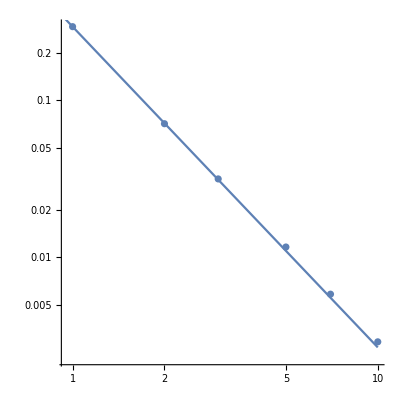

```mathematica
Show[ListLogLogPlot[{C0L0a[[1]],C0L0a[[2]],,C0L0a[[3]],C0L0a[[4]],C0L0a[[5]],C0L0a[[6]]},AspectRatio->1],LogLogPlot[0.29435079478442455 (1/a)^2.0415868706626115,{a,0,10}]]
```

```mathematica
C0L2=Import["C0L2.txt","Table"];
C0L2//MatrixForm
```

(1 | 0.264274 | 0.000310412
2 | 0.0662901 | 0.0000590701
3 | 0.0295386 | 0.0000184705
5 | 0.0106826 | 6.54092×10^-6
7 | 0.00545891 | 6.38016×10^-6
10 | 0.00270384 | 5.51069×10^-6)

```mathematica
ScientificForm[({{1, 0.2642740146757917, 0.00031041179368980037}, {2, 0.06629008690701141, 0.0000590700559035265}, {3, 0.029538618641291873, 0.000018470539558528764}, {5, 0.010682586536576744, 6.540920069331594*^-6}, {7, 0.005458909501348695, 6.380163342994563*^-6}, {10, 0.0027038438689069386, 5.51069209789704*^-6}})//MatrixForm]
```

(1 | 2.64274×10^-1 | 3.10412×10^-4
2 | 6.62901×10^-2 | 5.90701×10^-5
3 | 2.95386×10^-2 | 1.84705×10^-5
5 | 1.06826×10^-2 | 6.54092×10^-6
7 | 5.45891×10^-3 | 6.38016×10^-6
10 | 2.70384×10^-3 | 5.51069×10^-6)

```mathematica
ScientificForm[({{1, 0.2642740146757917, 0.00031041179368980037}, {2, 0.06629008690701141, 0.0000590700559035265}, {3, 0.029538618641291873, 0.000018470539558528764}, {5, 0.010682586536576744, 6.540920069331594*^-6}, {7, 0.005458909501348695, 6.380163342994563*^-6}, {10, 0.0027038438689069386, 5.51069209789704*^-6}})//MatrixForm]
```

(1 | 2.64274×10^-1 | 3.10412×10^-4
2 | 6.62901×10^-2 | 5.90701×10^-5
3 | 2.95386×10^-2 | 1.84705×10^-5
5 | 1.06826×10^-2 | 6.54092×10^-6
7 | 5.45891×10^-3 | 6.38016×10^-6
10 | 2.70384×10^-3 | 5.51069×10^-6)

```mathematica
C0L2a=({{1, 0.2642740146757917}, {2, 0.06629008690701141}, {3, 0.029538618641291873}, {5, 0.010682586536576744}, {7, 0.005458909501348695}, {10, 0.0027038438689069386}});
```

```mathematica
C0L2error={0.00031041179368980037,0.0000590700559035265,0.000018470539558528764,6.540920069331594*^-6,6.380163342994563*^-6,5.51069209789704*^-6}
```

{0.000310412,0.0000590701,0.0000184705,6.54092×10^-6,6.38016×10^-6,5.51069×10^-6}

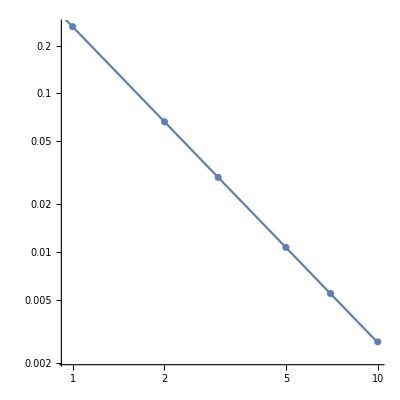

```mathematica
Show[ListLogLogPlot[{C0L2a[[1]],C0L2a[[2]],,C0L2a[[3]],C0L2a[[4]],C0L2a[[5]],C0L2a[[6]]},AspectRatio->1],LogLogPlot[0.26427141245400587 (1/a)^1.9947554712636948,{a,0,10}]]
```

```mathematica
fitC0L0=NonlinearModelFit[C0L0a,(A/a)^α,{α,A},{a},Weights->1/C0L0error^2]
fitC0L2=NonlinearModelFit[C0L2a,(A/a)^α,{α,A},{a},Weights->1/C0L2error^2]
```

FittedModel[0.282449 (1/a)^1.99351]

FittedModel[0.263809 (1/a)^1.99235]

```mathematica
FittedModel[0.29435079478442455 (1/a)^2.0415868706626115];{0.29435079478442455 (1/a)^2.0415868706626115,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {α, 2.0415868706626115, 0.007671177892429894, 266.13733891861625, 1.1958787088439055*^-9}, {A, 0.5493412117875611, 0.0014091227809281811, 389.84623570255053, 2.5975195190723774*^-10}}};
{0.28285887485132460 (1/a)^1.9946166104401340,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {α, 1.994616610440134, 0.0025858907855580483, 771.346037342287, 1.694920658629379*^-11}, {A, 0.5309392222493219, 0.001543993746140485, 343.8739461066526, 4.2907150787876987*^-10}}};
FittedModel[0.26427141245400587 (1/a)^1.9947554712636948];
{0.26427141245400587 (1/a)^1.9947554712636948,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {α, 1.9947554712636948, 0.0003667260116367323, 5439.36183408675, 6.854240738140632*^-15}, {A, 0.5131748121941148, 0.0000711423858678036, 7213.348356740431, 2.216172542389822*^-15}}};
{0.26380929349686900 (1/a)^1.9923508787279258,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {α, 1.9923508787279258, 0.0012608800857902217, 1580.1271676673955, 9.624583182095*^-13}, {A, 0.5123115429579406, 0.0006373583612523674, 803.8045377662921, 1.4372918228785758*^-11}}};
```

```mathematica
fitC0L0[{"BestFit","ParameterTable"}]
fitC0L2[{"BestFit","ParameterTable"}]
```

{0.282449 (1/a)^1.99351, | Estimate | Standard Error | t-Statistic | P-Value
α | 1.99351 | 0.0031539 | 632.079 | 3.75888×10^-11
A | 0.530367 | 0.00189821 | 279.404 | 9.84432×10^-10}

{0.263809 (1/a)^1.99235, | Estimate | Standard Error | t-Statistic | P-Value
α | 1.99235 | 0.00126088 | 1580.13 | 9.62458×10^-13
A | 0.512312 | 0.000637358 | 803.805 | 1.43729×10^-11}

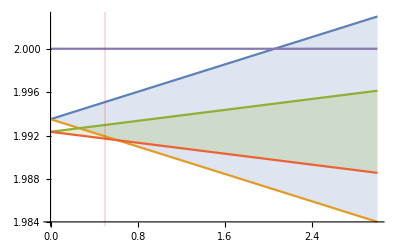

```mathematica
Plot[{1.9935135470323024+0.0031538981673576326x,1.9935135470323024-0.0031538981673576326x,1.9923508787279258+0.0012608800857902217x,1.9923508787279258-0.0012608800857902217x,2},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{.5,Red}},None}]
```

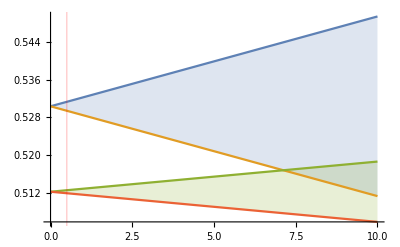

```mathematica
Plot[{0.5303670532766697+0.0018982109269868564x,0.5303670532766697-0.0018982109269868564x,0.5123115429579406+0.0006373583612523674x,0.5123115429579406-0.0006373583612523674x},{x,0,10},Filling->{1-> {2},3-> {4}},GridLines->{{{.5,Red}},None}]
```

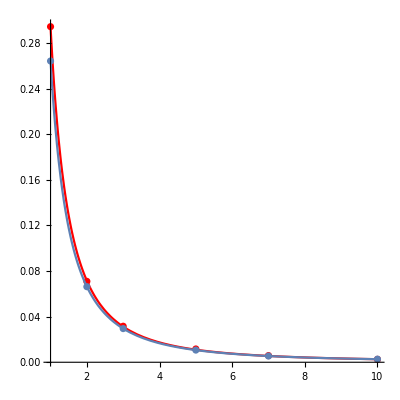

```mathematica
Show[Plot[0.29435079478442455 (1/a)^2.0415868706626115,{a,1,10},PlotStyle->Red,PlotRange->All,AspectRatio->1],ListPlot[{C0L0a[[1]],C0L0a[[2]],,C0L0a[[3]],C0L0a[[4]],C0L0a[[5]],C0L0a[[6]]},AspectRatio->1,PlotStyle->Red,PlotRange->All],ListPlot[{C0L2a[[1]],C0L2a[[2]],,C0L2a[[3]],C0L2a[[4]],C0L2a[[5]],C0L2a[[6]]},AspectRatio->1],Plot[0.26427141245400587 (1/a)^1.9947554712636948,{a,1,10},PlotRange->All]]
```

```mathematica
G0L0=Import["G0L0.txt","Table"];
G0L0//MatrixForm
```

(1 | 4.04368 | 0.00692816
2 | 4.02686 | 0.00373558
3 | 4.02787 | 0.000513577
5 | 4.04511 | 0.00897594
7 | 4.0328 | 0.000448896
10 | 4.0416 | 0.00219885)

```mathematica
G0L0a=({{1, 4.043684053999609}, {2, 4.026857247682726}, {3, 4.027874351030729}, {5, 4.045109842784561}, {7, 4.032800591268313}, {10, 4.04159898758259}});
```

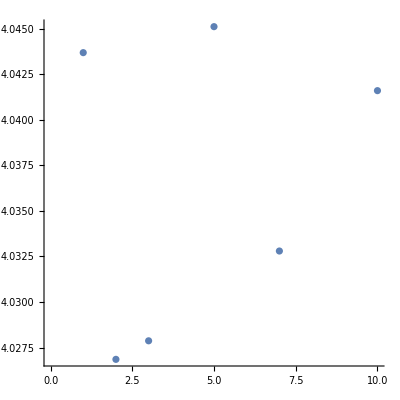

```mathematica
ListPlot[{G0L0a[[1]],G0L0a[[2]],G0L0a[[3]],G0L0a[[4]],G0L0a[[5]],G0L0a[[6]]},AspectRatio->1]
```

```mathematica
G0L2=Import["G0L2.txt","Table"];
G0L2//MatrixForm
```

(1 | 8.04931 | 0.00104202
2 | 8.05427 | 0.000790535
3 | 8.05824 | 0.000554752
5 | 8.06512 | 0.000543231
7 | 8.06894 | 0.00103694
10 | 8.08187 | 0.00180833)

```mathematica
G0L2a=({{1, 8.049309351311148}, {2, 8.054270500783167}, {3, 8.058238938726907}, {5, 8.065121883163535}, {7, 8.068942885488093}, {10, 8.081868039391335}});
```

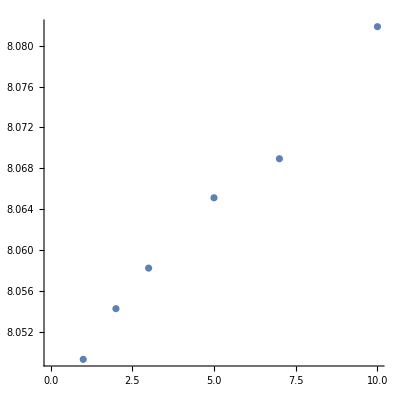

```mathematica
ListPlot[{G0L2a[[1]],G0L2a[[2]],G0L2a[[3]],G0L2a[[4]],G0L2a[[5]],G0L2a[[6]]},AspectRatio->1]
```

```mathematica
fitG0L0=NonlinearModelFit[G0L0a,(B+A a),{A,B},{a}]
fitG0L2=NonlinearModelFit[G0L2a,(B+A a),{A,B},{a}]
```

FittedModel[4.03346+0.000613625 a]

FittedModel[8.04695+0.00342936 a]

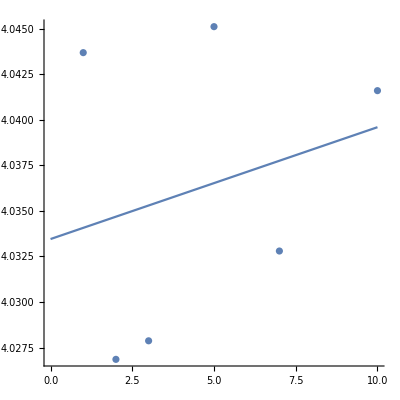

```mathematica
Show[ListPlot[{G0L0a[[1]],G0L0a[[2]],G0L0a[[3]],G0L0a[[4]],G0L0a[[5]],G0L0a[[6]]},AspectRatio->1],Plot[4.033457263683619+0.0006136247230993833 a,{a,0,10}]]
```

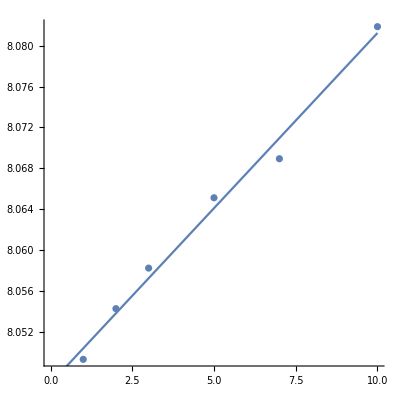

```mathematica
Show[ListPlot[{G0L2a[[1]],G0L2a[[2]],G0L2a[[3]],G0L2a[[4]],G0L2a[[5]],G0L2a[[6]]},AspectRatio->1],Plot[8.046954940769476+0.003429355508831901 a,{a,0,10}]]
```

```mathematica
fitG0L0[{"BestFit","ParameterTable"}]
fitG0L2[{"BestFit","ParameterTable"}]
```

{4.03346+0.000613625 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.000613625 | 0.00116457 | 0.526909 | 0.626125
B | 4.03346 | 0.00651884 | 618.739 | 4.09369×10^-11}

{8.04695+0.00342936 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00342936 | 0.000185026 | 18.5344 | 0.0000498714
B | 8.04695 | 0.00103571 | 7769.54 | 1.64653×10^-15}

```mathematica
fitC0L0[{"BestFit","ParameterTable"}]
fitC0L2[{"BestFit","ParameterTable"}]
fitG0L0[{"BestFit","ParameterTable"}]
fitG0L2[{"BestFit","ParameterTable"}]
```

{0.282449 (1/a)^1.99351, | Estimate | Standard Error | t-Statistic | P-Value
α | 1.99351 | 0.0031539 | 632.079 | 3.75888×10^-11
A | 0.530367 | 0.00189821 | 279.404 | 9.84432×10^-10}

{0.263809 (1/a)^1.99235, | Estimate | Standard Error | t-Statistic | P-Value
α | 1.99235 | 0.00126088 | 1580.13 | 9.62458×10^-13
A | 0.512312 | 0.000637358 | 803.805 | 1.43729×10^-11}

{4.03346+0.000613625 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.000613625 | 0.00116457 | 0.526909 | 0.626125
B | 4.03346 | 0.00651884 | 618.739 | 4.09369×10^-11}

{8.04695+0.00342936 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00342936 | 0.000185026 | 18.5344 | 0.0000498714
B | 8.04695 | 0.00103571 | 7769.54 | 1.64653×10^-15}

## Example

```mathematica
fileL0=Import["fileL0.txt","Table"];
fileL0//MatrixForm
```

(1 | 4. | 2.53974×10^-8
1 | 3.33333 | 4.16824×10^-7
1 | 2.85714 | 2.78958×10^-6
1 | 2.5 | 0.0000120918
1 | 2.22222 | 0.0000367784
1 | 2. | 0.0000905161
2 | 4. | 7.13223×10^-9
2 | 3.33333 | 1.02927×10^-7
2 | 2.85714 | 7.179×10^-7
2 | 2.5 | 2.99848×10^-6
2 | 2.22222 | 9.23142×10^-6
2 | 2. | 0.0000225623
3 | 4. | 3.15043×10^-9
3 | 3.33333 | 4.68115×10^-8
3 | 2.85714 | 3.18026×10^-7
3 | 2.5 | 1.3387×10^-6
3 | 2.22222 | 4.09552×10^-6
3 | 2. | 0.0000100257
5 | 4. | 9.86999×10^-10
5 | 3.33333 | 1.32433×10^-8
5 | 2.85714 | 1.09754×10^-7
5 | 2.5 | 4.67946×10^-7
5 | 2.22222 | 1.45688×10^-6
5 | 2. | 3.56891×10^-6
7 | 4. | 5.48481×10^-10
7 | 3.33333 | 8.46152×10^-9
7 | 2.85714 | 5.79094×10^-8
7 | 2.5 | 2.44125×10^-7
7 | 2.22222 | 7.47993×10^-7
7 | 2. | 1.83301×10^-6
10 | 4. | 2.59171×10^-10
10 | 3.33333 | 4.06583×10^-9
10 | 2.85714 | 2.81035×10^-8
10 | 2.5 | 1.19031×10^-7
10 | 2.22222 | 3.64543×10^-7
10 | 2. | 8.95646×10^-7)

```mathematica
fileL0a=({{4., 2.591709583892897*^-10}, {3.3333333333333335, 4.065830200055039*^-9}, {2.857142857142857, 2.810345426270042*^-8}, {2.5, 1.1903100946511252*^-7}, {2.2222222222222223, 3.645430694736472*^-7}, {2., 8.956457132140164*^-7}});
```

```mathematica
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{0,10,10,10,10,10}]
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{10,0,10,10,10,10}]
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{10,10,0,10,10,10}]
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{10,10,10,0,10,10}]
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{10,10,10,10,0,10}]
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv},Weights->{10,10,10,10,10,0}]
```

FittedModel[0.00290131 ⅇ^(-4.0416 ginv)]

FittedModel[0.00290124 ⅇ^(-4.04158 ginv)]

FittedModel[0.00290247 ⅇ^(-4.04179 ginv)]

FittedModel[0.00291824 ⅇ^(-4.04448 ginv)]

FittedModel[0.00287333 ⅇ^(-4.03672 ginv)]

FittedModel[0.0028335 ⅇ^(-4.03126 ginv)]

```mathematica
filefitL0a=NonlinearModelFit[fileL0a,A^2 ⅇ^(-G ginv),{A,G},{ginv}]
filefitL0a[{"BestFit","ParameterTable"}]
```

FittedModel[0.00290132 ⅇ^(-4.0416 ginv)]

{0.00290132 ⅇ^(-4.0416 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0538639 | 0.000120906 | 445.504 | 1.52311×10^-10
G | 4.0416 | 0.00219885 | 1838.05 | 5.25678×10^-13}

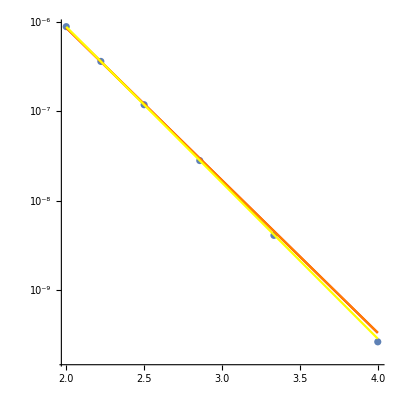

```mathematica
Show[ListLogPlot[{fileL0a[[1]],fileL0a[[2]],fileL0a[[3]],fileL0a[[4]],fileL0a[[5]],fileL0a[[6]]},AspectRatio->1],LogPlot[{0.002317370756471172 ⅇ^(-3.9434371519751257 ginv),0.0023073275534082806 ⅇ^(-3.9415424277582742 ginv),0.0028334996950234374 ⅇ^(-4.031256025101023 ginv)},{ginv,2,4},PlotStyle->{Red,Orange,Yellow,Green,Blue,Purple}]]
```

## Example

```mathematica
data={{0.9,6.1,9.5},{3.9,6.,9.7},{0.3,2.8,6.6},{1.,2.2,5.9},{1.8,2.4,7.2},{9.,1.7,7.},{7.9,8.,10.4},{4.9,3.9,9.},{2.3,2.6,7.4},{4.7,8.4,10.}};
data//MatrixForm
```

(0.9 | 6.1 | 9.5
3.9 | 6. | 9.7
0.3 | 2.8 | 6.6
1. | 2.2 | 5.9
1.8 | 2.4 | 7.2
9. | 1.7 | 7.
7.9 | 8. | 10.4
4.9 | 3.9 | 9.
2.3 | 2.6 | 7.4
4.7 | 8.4 | 10.)

```mathematica
errors={.4,.4,.2,.4,.1,.3,.1,.2,.2,.2};
errors//MatrixForm
```

(0.4
0.4
0.2
0.4
0.1
0.3
0.1
0.2
0.2
0.2)

```mathematica
nlm=NonlinearModelFit[data,a Log[b x+c y],{a,b,c},{x,y},Weights->1/errors^2]
nlm100=NonlinearModelFit[data,a Log[b x+c y],{a,b,c},{x,y},Weights->100/errors^2]
```

FittedModel[2.68807 Log[0.941344 x+5.01541 y]]

FittedModel[2.68807 Log[0.941344 x+5.01541 y]]

```mathematica
nlm[{"BestFit","ParameterTable"}]
nlm100[{"BestFit","ParameterTable"}]
```

{2.68807 Log[0.941344 x+5.01541 y], | Estimate | Standard Error | t-Statistic | P-Value
a | 2.68807 | 0.189622 | 14.176 | 2.06359×10^-6
b | 0.941344 | 0.480592 | 1.95872 | 0.0909916
c | 5.01541 | 1.1628 | 4.31323 | 0.00350919}

{2.68807 Log[0.941344 x+5.01541 y], | Estimate | Standard Error | t-Statistic | P-Value
a | 2.68807 | 0.189622 | 14.176 | 2.06359×10^-6
b | 0.941344 | 0.480592 | 1.95872 | 0.0909916
c | 5.01541 | 1.1628 | 4.31323 | 0.00350919}

```mathematica
{nlm["EstimatedVariance"],nlm100["EstimatedVariance"]}
```

{3.78528,378.528}

```mathematica
nlmvar1=NonlinearModelFit[data,a Log[b x+c y],{a,b,c},{x,y},Weights->1/errors^2,VarianceEstimatorFunction->(1&)]
```

FittedModel[2.68807 Log[0.941344 x+5.01541 y]]

```mathematica
nlmvar1[{"BestFit","ParameterTable"}]
```

{2.68807 Log[0.941344 x+5.01541 y], | Estimate | Standard Error | t-Statistic | P-Value
a | 2.68807 | 0.0974628 | 27.5805 | 2.11436×10^-8
b | 0.941344 | 0.247018 | 3.81084 | 0.00662066
c | 5.01541 | 0.597661 | 8.39173 | 0.0000670886}

## Big sizes convergence

```mathematica
NonlinearModelFit[({{1/10, 1.793118396840239 10^-08}, {1/20, 1.992068877035921 10^-08}, {1/30, 2.115149791851148 10^-08}, {1/40, 2.429353379320980 10^-08}, {1/50, 2.501136067154668 10^-08}}),a+c y,{a,c},{y}][{"BestFit","ParameterTable"}]
```

{2.53974×10^-8-8.18052×10^-8 y, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.53974×10^-8 | 1.29094×10^-9 | 19.6735 | 0.000286946
c | -8.18052×10^-8 | 2.38605×10^-8 | -3.42848 | 0.0415843}

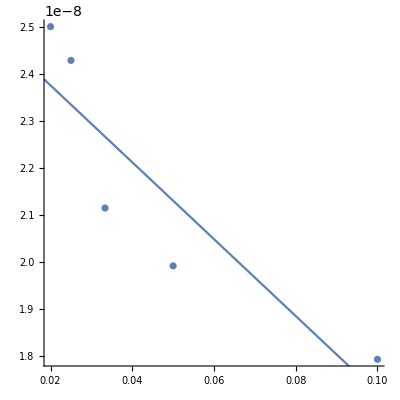

```mathematica
Show[ListPlot[({{1/10, 1.793118396840239 10^-08}, {1/20, 1.992068877035921 10^-08}, {1/30, 2.115149791851148 10^-08}, {1/40, 2.429353379320980 10^-08}, {1/50, 2.501136067154668 10^-08}}),AspectRatio->1],Plot[2.53974251155939*^-8-8.180522827418954*^-8 y,{y,0,.1}]]
```

## L0

```mathematica
dataL0=Import["fileL0.txt","Table"];
dataL0//MatrixForm
```

(1 | 4. | 2.92152×10^-8 | 7.89142×10^-11
1 | 3.33333 | 4.16824×10^-7 | 3.81478×10^-9
1 | 2.85714 | 2.78958×10^-6 | 4.01354×10^-8
1 | 2.5 | 0.0000120918 | 2.46623×10^-8
1 | 2.22222 | 0.0000367784 | 1.39409×10^-7
1 | 2. | 0.0000905161 | 1.11035×10^-7
2 | 4. | 7.13223×10^-9 | 5.98033×10^-11
2 | 3.33333 | 1.02927×10^-7 | 1.36963×10^-9
2 | 2.85714 | 7.179×10^-7 | 2.15358×10^-9
2 | 2.5 | 2.99848×10^-6 | 1.19969×10^-8
2 | 2.22222 | 9.23142×10^-6 | 1.73632×10^-8
2 | 2. | 0.0000225623 | 4.26516×10^-8
3 | 4. | 3.15043×10^-9 | 3.07837×10^-11
3 | 3.33333 | 4.68115×10^-8 | 2.32342×10^-10
3 | 2.85714 | 3.18026×10^-7 | 1.1854×10^-9
3 | 2.5 | 1.3387×10^-6 | 3.75348×10^-9
3 | 2.22222 | 4.09552×10^-6 | 9.31767×10^-9
3 | 2. | 0.0000100257 | 1.92782×10^-8
5 | 4. | 1.13815×10^-9 | 5.36147×10^-12
5 | 3.33333 | 1.67524×10^-8 | 9.92958×10^-11
5 | 2.85714 | 1.09754×10^-7 | 1.78933×10^-9
5 | 2.5 | 4.67946×10^-7 | 4.88222×10^-9
5 | 2.22222 | 1.45688×10^-6 | 6.45845×10^-9
5 | 2. | 3.56891×10^-6 | 1.65192×10^-8
7 | 4. | 5.48481×10^-10 | 1.57492×10^-11
7 | 3.33333 | 8.46152×10^-9 | 7.36518×10^-11
7 | 2.85714 | 5.79094×10^-8 | 3.12619×10^-10
7 | 2.5 | 2.44125×10^-7 | 1.06439×10^-9
7 | 2.22222 | 7.47993×10^-7 | 2.63191×10^-9
7 | 2. | 1.83301×10^-6 | 5.37979×10^-9
10 | 4. | 2.59171×10^-10 | 1.0806×10^-11
10 | 3.33333 | 4.06583×10^-9 | 5.98882×10^-11
10 | 2.85714 | 2.81035×10^-8 | 2.2815×10^-10
10 | 2.5 | 1.19031×10^-7 | 6.58314×10^-10
10 | 2.22222 | 3.64543×10^-7 | 5.58986×10^-10
10 | 2. | 8.95646×10^-7 | 3.18477×10^-9)

```mathematica
dataL0[[All,3]]/dataL0[[All,4]]//MatrixForm
```

(370.215
109.266
69.5042
490.294
263.817
815.201
119.262
75.1493
333.352
249.938
531.665
528.992
102.341
201.477
268.286
356.655
439.543
520.056
212.284
168.712
61.3377
95.8471
225.578
216.046
34.8261
114.885
185.24
229.357
284.201
340.722
23.9839
67.8903
123.18
180.812
652.151
281.228)

```mathematica
ScientificForm[TableForm[dataL0]]
```

1 | 4. | 2.92152×10^-8 | 7.89142×10^-11
1 | 3.33333 | 4.16824×10^-7 | 3.81478×10^-9
1 | 2.85714 | 2.78958×10^-6 | 4.01354×10^-8
1 | 2.5 | 1.20918×10^-5 | 2.46623×10^-8
1 | 2.22222 | 3.67784×10^-5 | 1.39409×10^-7
1 | 2. | 9.05161×10^-5 | 1.11035×10^-7
2 | 4. | 7.13223×10^-9 | 5.98033×10^-11
2 | 3.33333 | 1.02927×10^-7 | 1.36963×10^-9
2 | 2.85714 | 7.179×10^-7 | 2.15358×10^-9
2 | 2.5 | 2.99848×10^-6 | 1.19969×10^-8
2 | 2.22222 | 9.23142×10^-6 | 1.73632×10^-8
2 | 2. | 2.25623×10^-5 | 4.26516×10^-8
3 | 4. | 3.15043×10^-9 | 3.07837×10^-11
3 | 3.33333 | 4.68115×10^-8 | 2.32342×10^-10
3 | 2.85714 | 3.18026×10^-7 | 1.1854×10^-9
3 | 2.5 | 1.3387×10^-6 | 3.75348×10^-9
3 | 2.22222 | 4.09552×10^-6 | 9.31767×10^-9
3 | 2. | 1.00257×10^-5 | 1.92782×10^-8
5 | 4. | 1.13815×10^-9 | 5.36147×10^-12
5 | 3.33333 | 1.67524×10^-8 | 9.92958×10^-11
5 | 2.85714 | 1.09754×10^-7 | 1.78933×10^-9
5 | 2.5 | 4.67946×10^-7 | 4.88222×10^-9
5 | 2.22222 | 1.45688×10^-6 | 6.45845×10^-9
5 | 2. | 3.56891×10^-6 | 1.65192×10^-8
7 | 4. | 5.48481×10^-10 | 1.57492×10^-11
7 | 3.33333 | 8.46152×10^-9 | 7.36518×10^-11
7 | 2.85714 | 5.79094×10^-8 | 3.12619×10^-10
7 | 2.5 | 2.44125×10^-7 | 1.06439×10^-9
7 | 2.22222 | 7.47993×10^-7 | 2.63191×10^-9
7 | 2. | 1.83301×10^-6 | 5.37979×10^-9
10 | 4. | 2.59171×10^-10 | 1.0806×10^-11
10 | 3.33333 | 4.06583×10^-9 | 5.98882×10^-11
10 | 2.85714 | 2.81035×10^-8 | 2.2815×10^-10
10 | 2.5 | 1.19031×10^-7 | 6.58314×10^-10
10 | 2.22222 | 3.64543×10^-7 | 5.58986×10^-10
10 | 2. | 8.95646×10^-7 | 3.18477×10^-9

```mathematica
dataL0[[1;;6,2;;3]]//MatrixForm
dataL0[[1;;6,4]]//MatrixForm
```

(4. | 2.92152×10^-8
3.33333 | 4.16824×10^-7
2.85714 | 2.78958×10^-6
2.5 | 0.0000120918
2.22222 | 0.0000367784
2. | 0.0000905161)

(7.89142×10^-11
3.81478×10^-9
4.01354×10^-8
2.46623×10^-8
1.39409×10^-7
1.11035×10^-7)

```mathematica
NonlinearModelFit[dataL0[[01;;06,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[01;;06,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[07;;12,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[07;;12,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[13;;18,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[13;;18,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[19;;24,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[19;;24,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[25;;30,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[25;;30,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[31;;36,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[31;;36,4]]^2][{"BestFit","ParameterTable"}]
```

{0.280496 ⅇ^(-4.02004 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.280496 | 0.00196419 | 142.805 | 1.44223×10^-8
G | 4.02004 | 0.00283843 | 1416.29 | 1.49122×10^-12}

{0.0711557 ⅇ^(-4.02785 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0711557 | 0.000621435 | 114.502 | 3.48877×10^-8
G | 4.02785 | 0.00374853 | 1074.52 | 4.50088×10^-12}

{0.0315756 ⅇ^(-4.02743 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0315756 | 0.000138079 | 228.679 | 2.19378×10^-9
G | 4.02743 | 0.00183883 | 2190.21 | 2.60738×10^-13}

{0.0111328 ⅇ^(-4.02387 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0111328 | 0.000129866 | 85.7254 | 1.10999×10^-7
G | 4.02387 | 0.00400248 | 1005.34 | 5.8734×10^-12}

{0.0058615 ⅇ^(-4.0348 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0058615 | 0.0000584082 | 100.354 | 5.91186×10^-8
G | 4.0348 | 0.0042511 | 949.119 | 7.39377×10^-12}

{0.00291686 ⅇ^(-4.04418 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00291686 | 0.0000402462 | 72.4754 | 2.17189×10^-7
G | 4.04418 | 0.00615053 | 657.533 | 3.20977×10^-11}

```mathematica
G0L0=({{1, 4.020037237964663, 0.0028384283480775365}, {2, 4.027850346601865, 0.0037485254880071693}, {3, 4.027431524370874, 0.001838830624734447}, {5, 4.023866143435842, 0.00400247672554631}, {7, 4.034798551331821, 0.0042511001116005975}, {10, 4.044175706964364, 0.0061505288902013325}});
```

```mathematica
G0L0[[All,3]]
```

{0.00283843,0.00374853,0.00183883,0.00400248,0.0042511,0.00615053}

```mathematica
Needs["LinearRegression`"]
Regress[{{1, 4.032313105777002}, {2, 4.027850346601865}, {3, 4.027431524370874}, {5, 4.06301052826296}, {7, 4.034798551331821}, {10, 4.044175706964364}},{1,x},x,RegressionReport->{RSquared}]
```

General::obspkg: LinearRegression` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

{RSquared→0.186964}

```mathematica
NonlinearModelFit[G0L0[[All,1;;2]],A+α a,{A,α},{a},Weights->1/G0L0[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{4.01999+0.00210989 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 4.01999 | 0.00255665 | 1572.37 | 9.81598×10^-13
α | 0.00210989 | 0.000644822 | 3.27205 | 0.0307296}

```mathematica
ScientificForm[0.002109893534338766/4.019988578532697]
```

5.24851×10^-4

```mathematica
ScientificForm[{{0.0018968864057580992, 0.0008720075486863968}}]
```

{{1.89689×10^-3,8.72008×10^-4}}

```mathematica
4.02297508877706/0.0036774851652854753
0.0018968864057580992/0.0008720075486863968
```

1093.95

2.17531

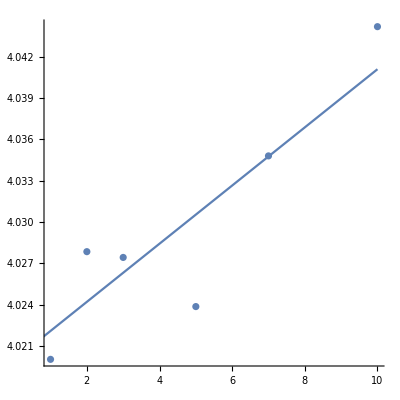

```mathematica
Show[ListPlot[G0L0[[All,1;;2]],AspectRatio->1,PlotRange->All],Plot[4.019988578532697+0.002109893534338766 a,{a,0,10},PlotRange->All]]
```

```mathematica
C0L0=({{1, 0.28049596064524174, 0.0019641867046810476}, {2, 0.07115574062511905, 0.0006214347853378486}, {3, 0.03157564332898384, 0.0001380787077899456}, {5, 0.011132807020840718, 0.00012986597508196597}, {7, 0.005861502382714182, 0.00005840823852944507}, {10, 0.0029168555089081494, 0.00004024616068829552}});
```

```mathematica
C0L0[[All,3]]
```

{0.00196419,0.000621435,0.000138079,0.000129866,0.0000584082,0.0000402462}

```mathematica
NonlinearModelFit[C0L0[[All,1;;2]],(A/a)^α,{A,α},{a},Weights->1/C0L0[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{0.280788 (1/a)^1.98966, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.528149 | 0.00291596 | 181.124 | 5.57395×10^-9
α | 1.98966 | 0.00621368 | 320.207 | 5.70692×10^-10}

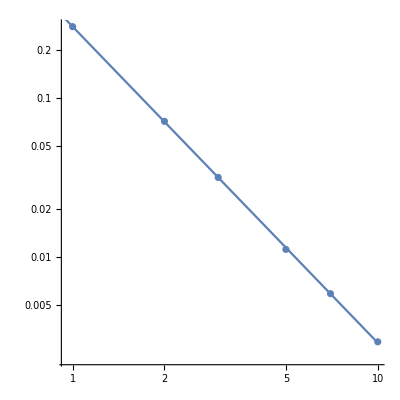

```mathematica
Show[ListLogLogPlot[C0L0[[All,1;;2]],AspectRatio->1],LogLogPlot[0.2807881109181846 (1/a)^1.9896615293714222,{a,0,10}]]
```

```mathematica
NonlinearModelFit[dataL0[[All,1;;3]],(A^2 ⅇ^(-G ginv))/a^2,{G,A},{a,ginv},Weights->1/dataL0[[All,4]]^2][{"BestFit","ParameterTable"}]
```

{(0.281561 ⅇ^(-4.02406 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
G | 4.02406 | 0.00241646 | 1665.27 | 4.34056×10^-85
A | 0.530623 | 0.00154074 | 344.394 | 8.05741×10^-62}

```mathematica
{(0.28571990773748085 ⅇ^(-4.030750613579991 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.030750613579991, 0.0032913115094340595, 1224.6639681556844, 1.4976510024368249*^-80}, {A, 0.5345277427201331, 0.0020041463256844265, 266.7109361576127, 4.778937116762248*^-58}}};
```

## L2

```mathematica
dataL2=Import["fileL2.txt","Table"];
dataL2//MatrixForm
```

(1 | 2. | 2.7127×10^-8 | 5.88125×10^-11
1 | 1.66667 | 3.95448×10^-7 | 1.19738×10^-9
1 | 1.42857 | 2.68217×10^-6 | 5.84284×10^-9
1 | 1.25 | 0.0000112794 | 1.93078×10^-8
1 | 1.11111 | 0.0000345039 | 4.93224×10^-8
2 | 2. | 6.55098×10^-9 | 5.27816×10^-11
2 | 1.66667 | 9.81992×10^-8 | 4.53553×10^-10
2 | 1.42857 | 6.67918×10^-7 | 2.03009×10^-9
2 | 1.25 | 2.8119×10^-6 | 6.55875×10^-9
2 | 1.11111 | 8.60731×10^-6 | 1.64221×10^-8
3 | 2. | 2.92241×10^-9 | 2.95438×10^-11
3 | 1.66667 | 4.34776×10^-8 | 2.2435×10^-10
3 | 1.42857 | 2.9587×10^-7 | 1.117×10^-9
3 | 1.25 | 1.24681×10^-6 | 3.54743×10^-9
3 | 1.11111 | 3.81851×10^-6 | 8.81845×10^-9
5 | 2. | 1.04595×10^-9 | 4.64577×10^-12
5 | 1.66667 | 1.55836×10^-8 | 8.60915×10^-11
5 | 1.42857 | 1.0589×10^-7 | 5.43316×10^-10
5 | 1.25 | 4.47072×10^-7 | 1.66031×10^-9
5 | 1.11111 | 1.37043×10^-6 | 4.09091×10^-9
7 | 2. | 5.05321×10^-10 | 1.51382×10^-11
7 | 1.66667 | 7.84517×10^-9 | 7.5651×10^-11
7 | 1.42857 | 5.38602×10^-8 | 2.97605×10^-10
7 | 1.25 | 2.27356×10^-7 | 1.00044×10^-9
7 | 1.11111 | 6.97338×10^-7 | 2.48916×10^-9
10 | 2. | 2.42988×10^-10 | 8.00953×10^-12
10 | 1.66667 | 3.78447×10^-9 | 5.33048×10^-11
10 | 1.42857 | 2.61431×10^-8 | 2.13215×10^-10
10 | 1.25 | 1.10834×10^-7 | 6.2397×10^-10
10 | 1.11111 | 3.40468×10^-7 | 1.48889×10^-9)

```mathematica
dataL2[[All,3]]/dataL2[[All,4]]//MatrixForm
```

(461.246
330.261
459.053
584.187
699.559
124.115
216.511
329.008
428.725
524.131
98.9178
193.794
264.878
351.468
433.014
225.141
181.012
194.895
269.27
334.994
33.3805
103.702
180.979
227.256
280.15
30.3374
70.9967
122.614
177.627
228.673)

```mathematica
dataL2[[All,3]]+a dataL2[[All,4]]
```

```mathematica
ScientificForm[TableForm[{dataL2[[All,1]],dataL2[[All,2]],dataL2[[All,3]]+a dataL2[[All,4]]}ᵀ]]
```

1 | 2. | 2.7127×10^-8+(5.88125×10^-11) a
1 | 1.66667 | 3.95448×10^-7+(1.19738×10^-9) a
1 | 1.42857 | 2.68217×10^-6+(5.84284×10^-9) a
1 | 1.25 | 1.12794×10^-5+(1.93078×10^-8) a
1 | 1.11111 | 3.45039×10^-5+(4.93224×10^-8) a
2 | 2. | 6.55098×10^-9+(5.27816×10^-11) a
2 | 1.66667 | 9.81992×10^-8+(4.53553×10^-10) a
2 | 1.42857 | 6.67918×10^-7+(2.03009×10^-9) a
2 | 1.25 | 2.8119×10^-6+(6.55875×10^-9) a
2 | 1.11111 | 8.60731×10^-6+(1.64221×10^-8) a
3 | 2. | 2.92241×10^-9+(2.95438×10^-11) a
3 | 1.66667 | 4.34776×10^-8+(2.2435×10^-10) a
3 | 1.42857 | 2.9587×10^-7+(1.117×10^-9) a
3 | 1.25 | 1.24681×10^-6+(3.54743×10^-9) a
3 | 1.11111 | 3.81851×10^-6+(8.81845×10^-9) a
5 | 2. | 1.04595×10^-9+(4.64577×10^-12) a
5 | 1.66667 | 1.55836×10^-8+(8.60915×10^-11) a
5 | 1.42857 | 1.0589×10^-7+(5.43316×10^-10) a
5 | 1.25 | 4.47072×10^-7+(1.66031×10^-9) a
5 | 1.11111 | 1.37043×10^-6+(4.09091×10^-9) a
7 | 2. | 5.05321×10^-10+(1.51382×10^-11) a
7 | 1.66667 | 7.84517×10^-9+(7.5651×10^-11) a
7 | 1.42857 | 5.38602×10^-8+(2.97605×10^-10) a
7 | 1.25 | 2.27356×10^-7+(1.00044×10^-9) a
7 | 1.11111 | 6.97338×10^-7+(2.48916×10^-9) a
10 | 2. | 2.42988×10^-10+(8.00953×10^-12) a
10 | 1.66667 | 3.78447×10^-9+(5.33048×10^-11) a
10 | 1.42857 | 2.61431×10^-8+(2.13215×10^-10) a
10 | 1.25 | 1.10834×10^-7+(6.2397×10^-10) a
10 | 1.11111 | 3.40468×10^-7+(1.48889×10^-9) a

```mathematica
dataL2[[1;;6,2;;3]]//MatrixForm
dataL2[[1;;6,4]]//MatrixForm
```

(2. | 2.7127×10^-8
1.66667 | 3.95448×10^-7
1.42857 | 2.68217×10^-6
1.25 | 0.0000112794
1.11111 | 0.0000345039
2. | 6.55098×10^-9)

(5.88125×10^-11
1.19738×10^-9
5.84284×10^-9
1.93078×10^-8
4.93224×10^-8
5.27816×10^-11)

```mathematica
NonlinearModelFit[dataL2[[01;;05,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[01;;05,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[06;;10,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[06;;10,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[11;;15,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[11;;15,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[16;;20,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[16;;20,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[21;;25,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[21;;25,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[26;;30,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[26;;30,4]]^2][{"BestFit","ParameterTable"}]
```

{0.261929 ⅇ^(-8.04183 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.261929 | 0.000439774 | 595.599 | 1.04377×10^-8
G | 8.04183 | 0.00118833 | 6767.34 | 7.1157×10^-12}

{0.0669686 ⅇ^(-8.06257 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0669686 | 0.000729218 | 91.8361 | 2.84606×10^-6
G | 8.06257 | 0.0084716 | 951.718 | 2.55826×10^-9}

{0.0296686 ⅇ^(-8.06177 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0296686 | 0.000194117 | 152.839 | 6.17592×10^-7
G | 8.06177 | 0.00507877 | 1587.35 | 5.51385×10^-10}

{0.0107854 ⅇ^(-8.07279 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0107854 | 0.0000768966 | 140.258 | 7.99107×10^-7
G | 8.07279 | 0.0049972 | 1615.46 | 5.23094×10^-10}

{0.00554784 ⅇ^(-8.08231 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00554784 | 0.000100733 | 55.0747 | 0.0000131856
G | 8.08231 | 0.0143748 | 562.253 | 1.24071×10^-8}

{0.00278251 ⅇ^(-8.10605 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00278251 | 0.000056224 | 49.4898 | 0.0000181671
G | 8.10605 | 0.016242 | 499.079 | 1.77401×10^-8}

```mathematica
G0L2=({{1, 8.041832777558335, 0.0011883306349949082}, {2, 8.06256602900104, 0.008471595669122695}, {3, 8.061769210078928, 0.005078771721502192}, {5, 8.07279348163923, 0.0049972022054462625}, {7, 8.082306098602958, 0.014374843573010025}, {10, 8.106047313745172, 0.016242019338286826}});
```

```mathematica
Needs["LinearRegression`"]
Regress[{{1, 8.041832777558335}, {2, 8.06256602900104}, {3, 8.061769210078928}, {5, 8.07279348163923}, {7, 8.082306098602958}, {10, 8.106047313745172}},{1,x},x,RegressionReport->{RSquared}]
```

General::obspkg: LinearRegression` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RSquared::shdw: Symbol RSquared appears in multiple contexts {RegressionCommon`,Global`}; definitions in context RegressionCommon` may shadow or be shadowed by other definitions.

{RSquared→0.948556}

```mathematica
NonlinearModelFit[G0L2[[All,1;;2]],A+α a,{A,α},{a},Weights->1/G0L2[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{8.03441+0.00778221 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 8.03441 | 0.00154081 | 5214.4 | 8.11584×10^-15
α | 0.00778221 | 0.000839023 | 9.27532 | 0.000751466}

```mathematica
ScientificForm[0.0077822086177004295/8.034410086348137]
```

9.6861×10^-4

```mathematica
ScientificForm[{{0.0077822086177004295, 0.0008390232365048055}}]
```

{{7.78221×10^-3,8.39023×10^-4}}

```mathematica
8.034410086348137/0.001540811617299269
0.0077822086177004295/0.0008390232365048055
```

5214.4

9.27532

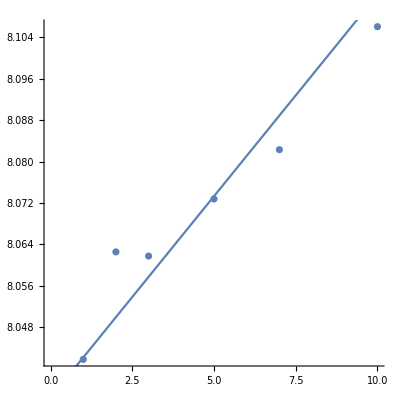

```mathematica
Show[ListPlot[G0L2[[All,1;;2]],AspectRatio->1],Plot[8.034410086348137+0.0077822086177004295 a,{a,0,10}]]
```

```mathematica
C0L2=({{1, 0.26192867507438883, 0.00043977371615375676}, {2, 0.06696857669536116, 0.0007292181211831182}, {3, 0.029668617661489177, 0.0001941168380948426}, {5, 0.010785389667344533, 0.0000768965777220101}, {7, 0.00554783572302413, 0.00010073290880814306}, {10, 0.0027825148394452753, 0.00005622401983145206}});
```

```mathematica
1000C0L2//MatrixForm
G0L2//MatrixForm
```

(1000 | 261.929 | 0.439774
2000 | 66.9686 | 0.729218
3000 | 29.6686 | 0.194117
5000 | 10.7854 | 0.0768966
7000 | 5.54784 | 0.100733
10000 | 2.78251 | 0.056224)

(1 | 8.04183 | 0.00118833
2 | 8.06257 | 0.0084716
3 | 8.06177 | 0.00507877
5 | 8.07279 | 0.0049972
7 | 8.08231 | 0.0143748
10 | 8.10605 | 0.016242)

```mathematica
NonlinearModelFit[C0L2[[All,1;;2]],(A/a)^α,{A,α},{a},Weights->1/C0L2[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{0.261936 (1/a)^1.98052, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.508436 | 0.000499265 | 1018.37 | 5.57865×10^-12
α | 1.98052 | 0.00198037 | 1000.07 | 5.99824×10^-12}

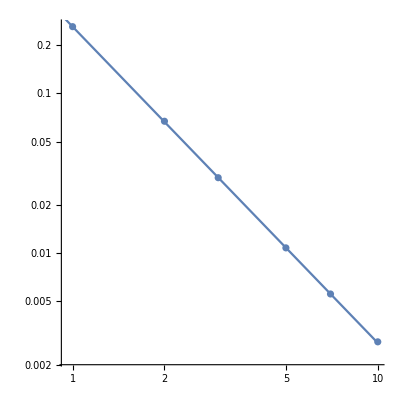

```mathematica
Show[ListLogLogPlot[C0L2[[All,1;;2]],AspectRatio->1],LogLogPlot[0.2619363341408044 (1/a)^1.980515652731696,{a,0,10}]]
```

```mathematica
NonlinearModelFit[dataL2[[All,1;;3]],(A^2 ⅇ^(-G ginv))/a^2,{G,A},{a,ginv},Weights->1/dataL2[[All,4]]^2][{"BestFit","ParameterTable"}]
```

{(0.2637 ⅇ^(-8.05038 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
G | 8.05038 | 0.00508591 | 1582.88 | 7.08087×10^-71
A | 0.513518 | 0.00177189 | 289.814 | 3.11459×10^-50}

# Comparing L0 and L2

```mathematica
{(0.28571990773748085 ⅇ^(-4.030750613579991 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.030750613579991, 0.0032913115094340595, 1224.6639681556844, 1.4976510024368249*^-80}, {A, 0.5345277427201331, 0.0020041463256844265, 266.7109361576127, 4.778937116762248*^-58}}};
{(0.2637004421506521 ⅇ^(-8.050383600102412 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 8.050383600102412, 0.005085908841636671, 1582.88004185143, 7.080874644491508*^-71}, {A, 0.5135177135704786, 0.001771887916950576, 289.81388080925797, 3.114587677034216*^-50}}};
```

```mathematica
{0.28260486459800893 (1/a)^1.9914039761429185,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 0.53015798551308, 0.0040912534285322925, 129.58326702906555, 2.1270766819199266*^-8}, {α, 1.9914039761429185, 0.008251788486610265, 241.32998311508624, 1.768709094552371*^-9}}};
{0.2619363341408044 (1/a)^1.980515652731696,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 0.5084356242792902, 0.0004992649201494674, 1018.3684127598578, 5.578645672554518*^-12}, {α, 1.980515652731696, 0.001980373669386424, 1000.0716952297776, 5.9982396402658956*^-12}}};
```

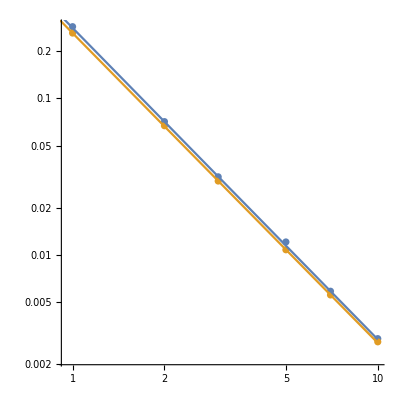

```mathematica
Show[ListLogLogPlot[{C0L0[[All,1;;2]],C0L2[[All,1;;2]]},AspectRatio->1],LogLogPlot[{0.28260486459800893 (1/a)^1.9914039761429185,0.2619363341408044 (1/a)^1.980515652731696},{a,0,10}]]
```

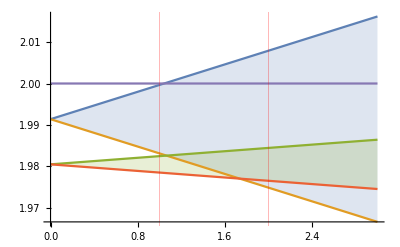

```mathematica
Plot[{1.9914039761429185+0.008251788486610265x,1.9914039761429185-0.008251788486610265x,1.980515652731696+0.001980373669386424x,1.980515652731696-0.001980373669386424x,2},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
{4.02297508877706+0.0018968864057580992 a,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 4.02297508877706, 0.0036774851652854753, 1093.9473330179335, 4.189509462772544*^-12}, {α, 0.0018968864057580992, 0.0008720075486863968, 2.17530961585779, 0.09524266752803368}}};
{8.034410086348137+0.0077822086177004295 a,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 8.034410086348137, 0.001540811617299269, 5214.401290944854, 8.115837473546208*^-15}, {α, 0.0077822086177004295, 0.0008390232365048055, 9.275319537179298, 0.0007514663847588728}}};
```

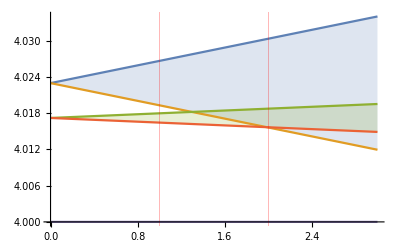

```mathematica
Plot[{4.02297508877706+0.0036774851652854753x,4.02297508877706-0.0036774851652854753x,(8.034410086348137+0.001540811617299269x)/2,(8.034410086348137-0.001540811617299269x)/2,4},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
{(0.2815610830507133 ⅇ^(-4.02406099634526 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.02406099634526, 0.0024164555528118016, 1665.274162259198, 4.34056254690846*^-85}, {A, 0.5306232967470551, 0.0015407441631660737, 344.39416317935473, 8.057408449328595*^-62}}};
{(0.2637004421506521 ⅇ^(-8.050383600102412 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 8.050383600102412, 0.005085908841636671, 1582.88004185143, 7.080874644491508*^-71}, {A, 0.5135177135704786, 0.001771887916950576, 289.81388080925797, 3.114587677034216*^-50}}};
```

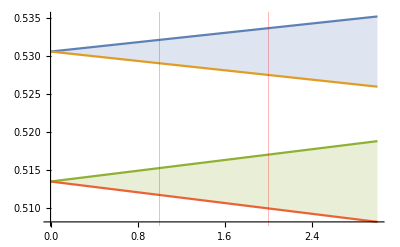

```mathematica
Plot[{0.5306232967470551+0.0015407441631660737x,0.5306232967470551-0.0015407441631660737x,0.5135177135704786+0.001771887916950576x,0.5135177135704786-0.001771887916950576x},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
4.02406099634526+±0.0024164555528118016
8.050383600102412/2±0.005085908841636671/2
```

4.02406+±0.00241646

4.02519±0.00254295

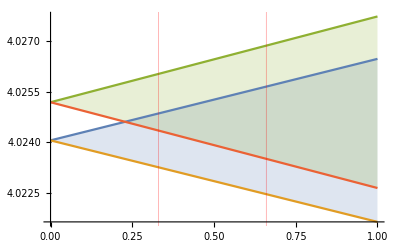

```mathematica
Plot[{4.02406099634526+0.0024164555528118016x,4.02406099634526-0.0024164555528118016x,(8.050383600102412+0.005085908841636671x)/2,(8.050383600102412-0.005085908841636671x)/2},{x,0,1},Filling->{1-> {2},3-> {4}},GridLines->{{{.33,Red},{.66,Red}},None}]
```

```mathematica
Manipulate[Plot[{b-a/x,b-a x,b},{x,0.1,10},PlotRange->All],{a,0,+10},{b,0.1,100}]
```